```mathematica
all6=Get["D:\\Saved\\allGraphs6-realnull.m"];
```

```mathematica
allGraphs=all6;
```

```mathematica
Length[all6]
```

53071

```mathematica
kkk=Select[Keys[all6],With[{g=all6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==14]&]
```

{7174452,7174450,7174444,7174426,7174372,7174210,7173724,7172266,7167892,7154770,7115404,6997306,6643012,5580130,2391484}

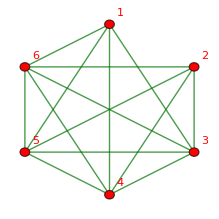

```mathematica
all6[2391484,"graph"]
```

```mathematica
all6[2391484,"colofourrealnull"]
```

-96 n123456+18 n12345x6+18 n12346x5+4 n1234x56-4 n1234x5x6+18 n12356x4+4 n1235x46-4 n1235x4x6+4 n1236x45-4 n1236x4x5+2 n123x456-n123x45x6-n123x46x5-n123x4x56+n123x4x5x6+18 n12456x3+4 n1245x36-4 n1245x3x6+4 n1246x35-4 n1246x3x5+2 n124x356-n124x35x6-n124x36x5-n124x3x56+n124x3x5x6+4 n1256x34-4 n1256x3x4+2 n125x346-n125x34x6-n125x36x4-n125x3x46+n125x3x4x6+2 n126x345-n126x34x5-n126x35x4-n126x3x45+n126x3x4x5+24 n13456x2+6 n1345x26-6 n1345x2x6+6 n1346x25-6 n1346x2x5+4 n134x256-2 n134x25x6-2 n134x26x5-2 n134x2x56+2 n134x2x5x6+6 n1356x24-6 n1356x2x4+4 n135x246-2 n135x24x6-2 n135x26x4-2 n135x2x46+2 n135x2x4x6+4 n136x245-2 n136x24x5-2 n136x25x4-2 n136x2x45+2 n136x2x4x5+6 n13x2456-2 n13x245x6-2 n13x246x5-n13x24x56+n13x24x5x6-2 n13x256x4-n13x25x46+n13x25x4x6-n13x26x45+n13x26x4x5-2 n13x2x456+n13x2x45x6+n13x2x46x5+n13x2x4x56-n13x2x4x5x6+6 n1456x23-6 n1456x2x3+4 n145x236-2 n145x23x6-2 n145x26x3-2 n145x2x36+2 n145x2x3x6+4 n146x235-2 n146x23x5-2 n146x25x3-2 n146x2x35+2 n146x2x3x5+6 n14x2356-2 n14x235x6-2 n14x236x5-n14x23x56+n14x23x5x6-2 n14x256x3-n14x25x36+n14x25x3x6-n14x26x35+n14x26x3x5-2 n14x2x356+n14x2x35x6+n14x2x36x5+n14x2x3x56-n14x2x3x5x6+4 n156x234-2 n156x23x4-2 n156x24x3-2 n156x2x34+2 n156x2x3x4+6 n15x2346-2 n15x234x6-2 n15x236x4-n15x23x46+n15x23x4x6-2 n15x246x3-n15x24x36+n15x24x3x6-n15x26x34+n15x26x3x4-2 n15x2x346+n15x2x34x6+n15x2x36x4+n15x2x3x46-n15x2x3x4x6+6 n16x2345-2 n16x234x5-2 n16x235x4-n16x23x45+n16x23x4x5-2 n16x245x3-n16x24x35+n16x24x3x5-n16x25x34+n16x25x3x4-2 n16x2x345+n16x2x34x5+n16x2x35x4+n16x2x3x45-n16x2x3x4x5+24 n1x23456-6 n1x2345x6-6 n1x2346x5-2 n1x234x56+2 n1x234x5x6-6 n1x2356x4-2 n1x235x46+2 n1x235x4x6-2 n1x236x45+2 n1x236x4x5-2 n1x23x456+n1x23x45x6+n1x23x46x5+n1x23x4x56-n1x23x4x5x6-6 n1x2456x3-2 n1x245x36+2 n1x245x3x6-2 n1x246x35+2 n1x246x3x5-2 n1x24x356+n1x24x35x6+n1x24x36x5+n1x24x3x56-n1x24x3x5x6-2 n1x256x34+2 n1x256x3x4-2 n1x25x346+n1x25x34x6+n1x25x36x4+n1x25x3x46-n1x25x3x4x6-2 n1x26x345+n1x26x34x5+n1x26x35x4+n1x26x3x45-n1x26x3x4x5-6 n1x2x3456+2 n1x2x345x6+2 n1x2x346x5+n1x2x34x56-n1x2x34x5x6+2 n1x2x356x4+n1x2x35x46-n1x2x35x4x6+n1x2x36x45-n1x2x36x4x5+2 n1x2x3x456-n1x2x3x45x6-n1x2x3x46x5-n1x2x3x4x56+n1x2x3x4x5x6

```mathematica
Table[ListofVars[ all6[k,"colofour"]]/.demo6,{k,kkk}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
EdgeCount[CompleteGraph[6]]
```

15

```mathematica
atomKeys=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&];Length[atomKeys]
```

203

```mathematica
demo6=Table[allGraphs[k,"colofour"]->ChromaticPolynomial[ allGraphs[k,"graph"],4],{k,atomKeys}]
```

{v1x2x3x4x5x6→0,v1x2x3x4x56→0,v1x2x3x46x5→0,v1x2x3x45x6→0,v1x2x3x456→24,v1x2x36x4x5→0,v1x2x36x45→24,v1x2x35x4x6→0,v1x2x35x46→24,v1x2x356x4→24,v1x2x34x5x6→0,v1x2x34x56→24,v1x2x346x5→24,v1x2x345x6→24,v1x2x3456→24,v1x26x3x4x5→0,v1x26x3x45→24,v1x26x35x4→24,v1x26x34x5→24,v1x26x345→24,v1x25x3x4x6→0,v1x25x3x46→24,v1x25x36x4→24,v1x25x34x6→24,v1x25x346→24,v1x256x3x4→24,v1x256x34→24,v1x24x3x5x6→0,v1x24x3x56→24,v1x24x36x5→24,v1x24x35x6→24,v1x24x356→24,v1x246x3x5→24,v1x246x35→24,v1x245x3x6→24,v1x245x36→24,v1x2456x3→24,v1x23x4x5x6→0,v1x23x4x56→24,v1x23x46x5→24,v1x23x45x6→24,v1x23x456→24,v1x236x4x5→24,v1x236x45→24,v1x235x4x6→24,v1x235x46→24,v1x2356x4→24,v1x234x5x6→24,v1x234x56→24,v1x2346x5→24,v1x2345x6→24,v1x23456→12,v16x2x3x4x5→0,v16x2x3x45→24,v16x2x35x4→24,v16x2x34x5→24,v16x2x345→24,v16x25x3x4→24,v16x25x34→24,v16x24x3x5→24,v16x24x35→24,v16x245x3→24,v16x23x4x5→24,v16x23x45→24,v16x235x4→24,v16x234x5→24,v16x2345→12,v15x2x3x4x6→0,v15x2x3x46→24,v15x2x36x4→24,v15x2x34x6→24,v15x2x346→24,v15x26x3x4→24,v15x26x34→24,v15x24x3x6→24,v15x24x36→24,v15x246x3→24,v15x23x4x6→24,v15x23x46→24,v15x236x4→24,v15x234x6→24,v15x2346→12,v156x2x3x4→24,v156x2x34→24,v156x24x3→24,v156x23x4→24,v156x234→12,v14x2x3x5x6→0,v14x2x3x56→24,v14x2x36x5→24,v14x2x35x6→24,v14x2x356→24,v14x26x3x5→24,v14x26x35→24,v14x25x3x6→24,v14x25x36→24,v14x256x3→24,v14x23x5x6→24,v14x23x56→24,v14x236x5→24,v14x235x6→24,v14x2356→12,v146x2x3x5→24,v146x2x35→24,v146x25x3→24,v146x23x5→24,v146x235→12,v145x2x3x6→24,v145x2x36→24,v145x26x3→24,v145x23x6→24,v145x236→12,v1456x2x3→24,v1456x23→12,v13x2x4x5x6→0,v13x2x4x56→24,v13x2x46x5→24,v13x2x45x6→24,v13x2x456→24,v13x26x4x5→24,v13x26x45→24,v13x25x4x6→24,v13x25x46→24,v13x256x4→24,v13x24x5x6→24,v13x24x56→24,v13x246x5→24,v13x245x6→24,v13x2456→12,v136x2x4x5→24,v136x2x45→24,v136x25x4→24,v136x24x5→24,v136x245→12,v135x2x4x6→24,v135x2x46→24,v135x26x4→24,v135x24x6→24,v135x246→12,v1356x2x4→24,v1356x24→12,v134x2x5x6→24,v134x2x56→24,v134x26x5→24,v134x25x6→24,v134x256→12,v1346x2x5→24,v1346x25→12,v1345x2x6→24,v1345x26→12,v13456x2→12,v12x3x4x5x6→0,v12x3x4x56→24,v12x3x46x5→24,v12x3x45x6→24,v12x3x456→24,v12x36x4x5→24,v12x36x45→24,v12x35x4x6→24,v12x35x46→24,v12x356x4→24,v12x34x5x6→24,v12x34x56→24,v12x346x5→24,v12x345x6→24,v12x3456→12,v126x3x4x5→24,v126x3x45→24,v126x35x4→24,v126x34x5→24,v126x345→12,v125x3x4x6→24,v125x3x46→24,v125x36x4→24,v125x34x6→24,v125x346→12,v1256x3x4→24,v1256x34→12,v124x3x5x6→24,v124x3x56→24,v124x36x5→24,v124x35x6→24,v124x356→12,v1246x3x5→24,v1246x35→12,v1245x3x6→24,v1245x36→12,v12456x3→12,v123x4x5x6→24,v123x4x56→24,v123x46x5→24,v123x45x6→24,v123x456→12,v1236x4x5→24,v1236x45→12,v1235x4x6→24,v1235x46→12,v12356x4→12,v1234x5x6→24,v1234x56→12,v12346x5→12,v12345x6→12,v123456→4}

## From 5 edges to 4

```mathematica
HandleEdge[g_,e_]:={EdgeDelete[g,e],EdgeContract[g,e]}
```

```mathematica
start=CompleteGraph[5,VertexLabels->"Name", ImageSize->100]
```

-Graphics-

```mathematica
HandleEdge[start,1<->2]
```

{-Graphics-,-Graphics-}

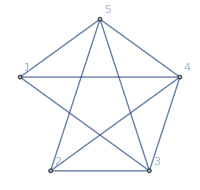
```mathematica
HandleEdge[-Graphics-,1<->3]
```

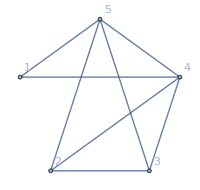
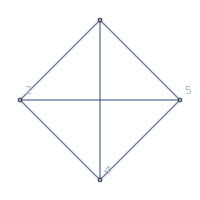

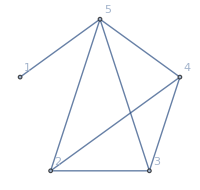
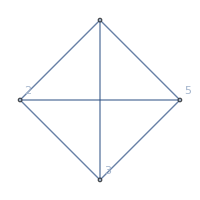

```mathematica
HandleEdge[-Graphics-,1<->4]
```

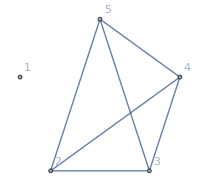
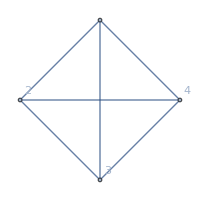

```mathematica
HandleEdge[-Graphics-,1<->5]
```

## From 6 edges to 5

```mathematica
HandleEdge[g_,e_]:={EdgeDelete[g,e],EdgeContract[g,e]}
```

```mathematica
start=CompleteGraph[6,VertexLabels->"Name", ImageSize->100]
```

-Graphics-

```mathematica
HandleEdge[start,1<->2]
```

{-Graphics-,-Graphics-}

```mathematica
HandleEdge[-Graphics-,1<->3]
```

{-Graphics-,-Graphics-}

```mathematica
HandleEdge[-Graphics-,1<->4]
```

{-Graphics-,-Graphics-}

```mathematica
HandleEdge[-Graphics-,1<->5]
```

{-Graphics-,-Graphics-}

```mathematica
HandleEdge[-Graphics-,1<->6]
```

{-Graphics-,-Graphics-}

## From 4 edges to 3

```mathematica
HandleEdge[g_,e_]:={EdgeDelete[g,e],EdgeContract[g,e]}
```

```mathematica
start=CompleteGraph[4,VertexLabels->"Name", ImageSize->100]
```

-Graphics-

```mathematica
HandleEdge[start,1<->2]
```

{-Graphics-,-Graphics-}

```mathematica
HandleEdge[-Graphics-,1<->3]
```

{-Graphics-,-Graphics-}

```mathematica
HandleEdge[-Graphics-,1<->4]
```

{-Graphics-,-Graphics-}

```mathematica
ChromaticPolynomial[CompleteGraph[2],4]
```

12

```mathematica
ChromaticPolynomial[CompleteGraph[3],4]
```

24

```mathematica
HandleVertex[g_,v_]:=Block[{h=g,edges=EdgeList[g,v<->_],e,result={g},f},
While[VertexDegree[h,v]≠0,
e=First[edges];
edges=Rest[edges];
f=EdgeContract[h,e];
h=EdgeDelete[h,e];
result=Append[result,{h,-f}]
];
result
]
```

```mathematica
HandleVertex[CompleteGraph[5,ImageSize->80,VertexLabels->"Name"],1]
```

{-Graphics-,{-Graphics-,--Graphics-},{-Graphics-,--Graphics-},{-Graphics-,--Graphics-},{-Graphics-,--Graphics-}}

```mathematica
HandleVertex[CompleteGraph[6,ImageSize->80,VertexLabels->"Name"],1]
```

{-Graphics-,{-Graphics-,--Graphics-},{-Graphics-,--Graphics-},{-Graphics-,--Graphics-},{-Graphics-,--Graphics-},{-Graphics-,--Graphics-}}

```mathematica
HandleVertex[EdgeAdd[CompleteGraph[5,ImageSize->80,VertexLabels->"Name"],{1<->6,6<->5}],1]
```

{-Graphics-,{-Graphics-,--Graphics-},{-Graphics-,--Graphics-},{-Graphics-,--Graphics-},{-Graphics-,--Graphics-},{-Graphics-,--Graphics-}}

```mathematica
ChromaticPolynomial[-Graphics-,x]//Factor
```

(-3+x) (-2+x)^2 (-1+x)^2 x

```mathematica
HandleVertex[CompleteGraph[3,ImageSize->80,VertexLabels->"Name"],1]
```

{-Graphics-,{-Graphics-,--Graphics-},{-Graphics-,--Graphics-}}

```mathematica
allGraphs[k5Key,"colofourrealnull"]
```

24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5

```mathematica
Table[If[MemberQ[allGraphs[k,"vertexsets"],{5}],k,0],{k,realyNullAtomKeys}]
```

{0,0,0,18,0,0,0,162,0,0,486,0,0,666,0,0,0,0,0,0,4374,0,0,4860,0,0,0,13122,0,0,13284,0,0,0,17514,0,0,39366,0,0,39384,0,0,0,43902,0,0,52974,0,0,57528,0}

```mathematica
Table[allGraphs[k,"graph"],{k,Select[realyNullAtomKeys,MemberQ[allGraphs[#,"vertexsets"],{5}]&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[allGraphs[k,"graph"],{k,Select[realyNullAtomKeys,!MemberQ[allGraphs[#,"vertexsets"],{5}]&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}